## Import raw coordinates

```mathematica
rawCoordinates = Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx"];
```

## Sticky DBScan

```mathematica
(*
Output: clusters for the sheep as traditional DBSCAN but with sheep tending to "stick" to the group they are already with. If r1=r2, equivalent to DBSCAN
Inputs: 
- pts (locations of the sheep, 2D, list of list)
- r1 (smaller of the two radii, sheep are considered together)
-r2(larger of the two radii, sheep are considered together only if they were in the same group in the last time step)
- k (minimum number of neighbors(including oneself) to be considered a core point)
- indexPrevClusters (Association from each cluster to the neighbors in the previous cluster)*)
dbscanSticky[pts_,{r1_,r2_},k_,indexPrevClusters_]:=
Module[{indexPts,nf,pointNeighbors,coreIndices,clusterCores,coreClusters,noncoreIndices,clusterNoncores},
(*Turn points into association with the correct index, delete missing points*)
indexPts=DeleteMissing[AssociationThread[Range[Length[pts]],pts],1,2];
(*Define nearest function*)
nf=Nearest[indexPts];
(*For each point, find its neighbors, considering whether they were neighbors in the previous time step or not*)
pointNeighbors=
Association[MapThread[
#2->With[{prevNeighbors=indexPrevClusters[#2]},
Select[#1,Function[n,
With[{d=EuclideanDistance[indexPts[#2],indexPts[n]]},
If[MemberQ[prevNeighbors,n],d≤r2,d≤r1]
]
]]
]&,
{nf[Values[indexPts],{All,r2}][[All,2;;]],Keys[indexPts]}
]];
(*Find all core points*)
coreIndices=Position[pointNeighbors,_?(Length[#]+1≥k&),{1},Heads->False][[All,1,1]];
(*Form the clusters just from the core points*)
clusterCores=
ConnectedComponents[
Catenate[MapThread[
Thread[#1->#2]&,{
coreIndices,
Select[MemberQ[coreIndices,#]&]/@Lookup[pointNeighbors,coreIndices]
}]]
];
coreClusters=Association[Catenate[MapIndexed[Thread[#1->First[#2]]&,clusterCores]]];
(*Consider all points that are not cores*)
noncoreIndices=Complement[Keys[indexPts],coreIndices];
(*if they could be in more than one cluster, chose randomly*)
clusterNoncores=Merge[Lookup[coreClusters,pointNeighbors[#],Nothing]->#&/@noncoreIndices,Identity];
KeyValueMap[
With[{c=RandomChoice[#1]},clusterCores[[c]]=Join[clusterCores[[c]],#2]]&,
KeyDrop[clusterNoncores,Key[{}]]
];
(*Return the full set of clusters, add an empty list if none of the sheep are alone*)
Append[clusterCores,Lookup[clusterNoncores,Key[{}],{}]]
]
```

## Test on one time snapshot

Pick a time step:

```mathematica
pts=rawCoordinates[[All,10000]];
```

```mathematica
ptsPrior=Association[#->{}&/@Range[Length[pts]]]
```

<|1→{},2→{},3→{},4→{},5→{},6→{},7→{},8→{},9→{},10→{},11→{},12→{},13→{},14→{},15→{},16→{},17→{},18→{},19→{},20→{},21→{},22→{},23→{},24→{},25→{},26→{},27→{},28→{},29→{},30→{},31→{},32→{},33→{},34→{},35→{},36→{},37→{},38→{},39→{},40→{},41→{},42→{},43→{},44→{},45→{},46→{},47→{},48→{},49→{},50→{},51→{}|>

Run, assuming no prior information on clusters, with r1=10, r2=15, k = 3,

```mathematica
testClustering = dbscanSticky[pts,{10,15},3, ptsPrior]
```

{{7,14,43,24,33,49,48,18,47,9,51},{12,39,37,38},{13,44,19},{21,23,36,32,30,46,27,6},{1,2,3,4,5,8,10,11,15,16,17,20,22,25,26,28,29,31,34,35,40,41,42,45}}

### Test a second step

```mathematica
pts2=rawCoordinates[[All,10001]];
pts2prior=Join[ptsPrior,Association[Catenate[Function[c,#->c&/@c]/@testClustering]]]
```

```mathematica
testClustering2=dbscanSticky[pts2,{10,15},3, pts2prior]
```

{{6,23,21,46,32,36,30,27},{7,43,14,24,33,49,47,18,48,9,51},{12,39,37,38},{13,44,19},{1,2,3,4,5,8,10,11,15,16,17,20,22,25,26,28,29,31,34,35,40,41,42,45}}

```mathematica
pts2prior
```

## Run for all sheep

```mathematica
fullDBScan[data_,{r1_,r2_},k_,{minTime_,maxTime_}]:=FoldPairList[With[{clustering=dbscanSticky[#2,{r1,r2},k,#1]},{clustering,Join[#1,Association[Catenate[Function[c,#->c&/@c]/@clustering]]]}]&,Association[#->{}&/@Range[Length[data]]],Transpose[data][[minTime;;maxTime]]]
```

```mathematica
DBSCAN30Sticky50 =fullDBScan[rawCoordinates,{30,50},2,{1,210351}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/DBSCAN30Sticky50.mx",DBSCAN30Sticky50];
```

```mathematica
DBSCAN3Sticky5 =fullDBScan[rawCoordinates,{3,5},2,{1,210351}];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/DBSCAN3Sticky5.mx",DBSCAN3Sticky5];
```

```mathematica
DBSCAN30Sticky50
```

{{{5,48,40,38,21,17,44,8,33,22,35},{}},{{2,22,18,8,25,38,31,20,19,46,9,23,4,41,10,51,40,14,34,21,29,44,16,24,3,47,36,48,17,5,42,45,27,33,35,7,12,39,26,37,11},{}},210348,{{5,51,40},{12,50,44},{2,7,8,16,21,31,39,46}}}
 |  |  |  |

```mathematica
DBSCAN30Sticky50LonelySheep=Join[Most[#],List/@Last[#]]&/@DBSCAN30Sticky50;
```

```mathematica
DBSCAN3Sticky5LonelySheep=Join[Most[#],List/@Last[#]]&/@DBSCAN3Sticky5;
```

```mathematica
GroupStability30Sticky50=GroupBy[Catenate[MapIndexed[#1->First[#2]&,DBSCAN30Sticky50LonelySheep,{2}]],First->Last,Join];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/groupStability30Sticky50.mx",GroupStability30Sticky50];
```

## Fission Fusion Graph Code

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]];
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]]
```

```mathematica
fullGraph30Sticky50=FindFissionFusionGraph[1,210350,0.8,DBSCAN30Sticky50LonelySheep];
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/StickyDBScan/fullGraph30Sticky50.mx",fullGraph30Sticky50];
```

## Plotting Graphs

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]/10,Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#],2]]]]/100}&/@VertexList[g]),Frame->True,FrameTicks->True,EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Large],None}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

#### 30-50 radius

```mathematica
DBSCAN30Sticky50
```

{{{5,48,40,38,21,17,44,8,33,22,35},{}},{{2,22,18,8,25,38,31,20,19,46,9,23,4,41,10,51,40,14,34,21,29,44,16,24,3,47,36,48,17,5,42,45,27,33,35,7,12,39,26,37,11},{}},210348,{{5,51,40},{7,8},{12,50,44},{16,39},{31,46},{2,21}}}
 |  |  |  |

```mathematica
DBSCAN30Sticky50LonelySheep[[;;2]]
```

{{{5,48,40,38,21,17,44,8,33,22,35}},{{2,22,18,8,25,38,31,20,19,46,9,23,4,41,10,51,40,14,34,21,29,44,16,24,3,47,36,48,17,5,42,45,27,33,35,7,12,39,26,37,11}}}

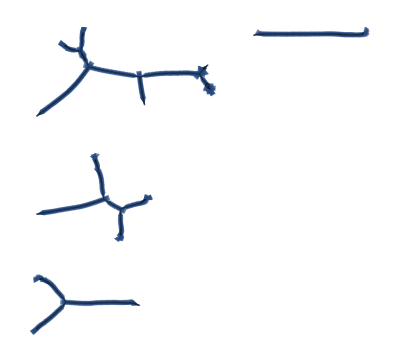

```mathematica
graph30Sticky50=FindFissionFusionGraph[700,800,0.8,DBSCAN30Sticky50LonelySheep]
```

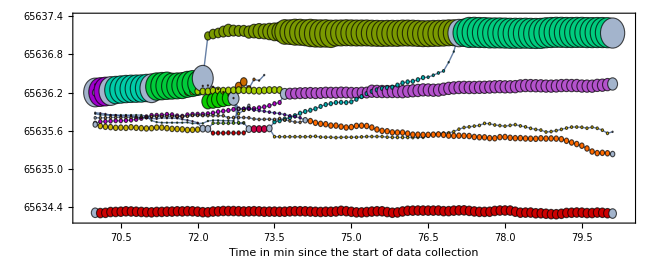

```mathematica
coloredGraph[graph30Sticky50,100]
```

```mathematica
dbScanHerds30=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds30.mx"];
```

```mathematica
dbScanHerds30LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds30;
```

```mathematica
g30=FindFissionFusionGraph[700,800,0.8,dbScanHerds30LonelySheep];
```

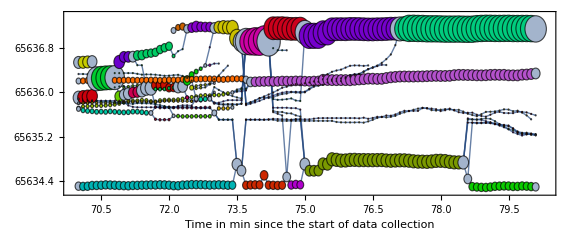

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
coloredGraph[g30,100]
```

### 3-5 radius

```mathematica
graph3Sticky5=FindFissionFusionGraph[700,800,0.8,DBSCAN3Sticky5LonelySheep];
```

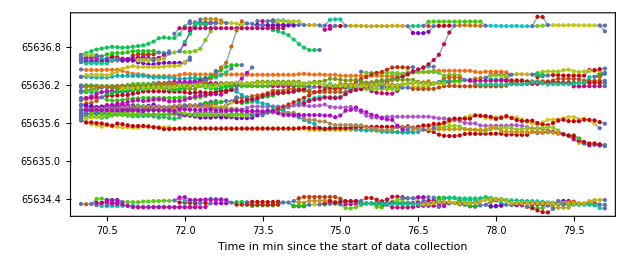

```mathematica
coloredGraph[graph3Sticky5,100]
```

## Merging and Splitting events

```mathematica
mergingEvents30Sticky50 =Select[VertexList[fullGraph30Sticky50],VertexInDegree[fullGraph30Sticky50,#]≥2&];
```

```mathematica
splittingEvents30Sticky50=Select[VertexList[fullGraph30Sticky50],VertexOutDegree[fullGraph30Sticky50,#]≥ 2&];
```

```mathematica
Length[mergingEvents30Sticky50]
Length[splittingEvents30Sticky50]
```

3343

3423

```mathematica
fullGraph30=FindFissionFusionGraph[1,210350,0.8,dbScanHerds30LonelySheep];
```

```mathematica
mergingEvents30 =Select[VertexList[fullGraph30],VertexInDegree[fullGraph30,#]≥2&];
```

```mathematica
splittingEvents30=Select[VertexList[fullGraph30],VertexOutDegree[fullGraph30,#]≥ 2&];
```

```mathematica
Length[mergingEvents30]
Length[splittingEvents30]
```

20508

20430

## Analysis of splitting and merging events

```mathematica
groupedMergingEvents30Sticky50=GroupBy[mergingEvents30Sticky50,Min[Length/@VertexInComponent[fullGraph30Sticky50,{#},{1}][[All,1]]]&];
```

```mathematica
mergingDistribution30Sticky50=Table[{x,Length[groupedMergingEvents30Sticky50[[Key[x]]]]},{x,1,24}]
```

{{1,2076},{2,5},{3,353},{4,265},{5,168},{6,121},{7,87},{8,60},{9,52},{10,27},{11,38},{12,25},{13,13},{14,16},{15,10},{16,9},{17,5},{18,2},{19,4},{20,2},{21,1},{22,4},{23,2},{24,2}}

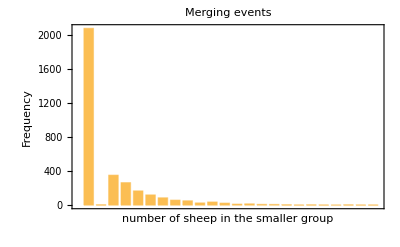

```mathematica
BarChart[mergingDistribution30Sticky50[[All,2]],Frame->True,FrameLabel->{"number of sheep in the smaller group","Frequency"},PlotLabel->"Merging events"]
```

## Symmetric Sticky

```mathematica
(*
Output: clusters for the sheep as traditional DBSCAN but with sheep tending to "stick" to the group they are already with. If r1=r2, equivalent to DBSCAN
Inputs: 
- pts (locations of the sheep, 2D, list of list)
- r1 (smaller of the two radii, sheep are considered together)
-r2(larger of the two radii, sheep are considered together only if they were in the same group in the last time step)
- k (minimum number of neighbors(including oneself) to be considered a core point)
- indexPrevClusters (Association from each cluster to the neighbors in the previous cluster)*)
dbscanSticky[pts_,{r1_,r2_},k_,indexPrevClusters_]:=
Module[{indexPts,nf,pointNeighbors,coreIndices,clusterCores,coreClusters,noncoreIndices,clusterNoncores},
(*Turn points into association with the correct index, delete missing points*)
indexPts=DeleteMissing[AssociationThread[Range[Length[pts]],pts],1,2];
(*Define nearest function*)
nf=Nearest[indexPts];
(*For each point, find its neighbors, considering whether they were neighbors in the previous time step or not*)
pointNeighbors=
Association[MapThread[
#2->With[{prevNeighbors=indexPrevClusters[#2]},
Select[#1,Function[n,
With[{d=EuclideanDistance[indexPts[#2],indexPts[n]]},
If[MemberQ[prevNeighbors,n],d≤r2,d≤r1]
]
]]
]&,
{nf[Values[indexPts],{All,r2}][[All,2;;]],Keys[indexPts]}
]];
(*Find all core points*)
coreIndices=Position[pointNeighbors,_?(Length[#]+1≥k&),{1},Heads->False][[All,1,1]];
(*Form the clusters just from the core points*)
clusterCores=
ConnectedComponents[
Catenate[MapThread[
Thread[#1->#2]&,{
coreIndices,
Select[MemberQ[coreIndices,#]&]/@Lookup[pointNeighbors,coreIndices]
}]]
];
coreClusters=Association[Catenate[MapIndexed[Thread[#1->First[#2]]&,clusterCores]]];
(*Consider all points that are not cores*)
noncoreIndices=Complement[Keys[indexPts],coreIndices];
(*if they could be in more than one cluster, chose randomly*)
clusterNoncores=Merge[Lookup[coreClusters,pointNeighbors[#],Nothing]->#&/@noncoreIndices,Identity];
KeyValueMap[
With[{c=RandomChoice[#1]},clusterCores[[c]]=Join[clusterCores[[c]],#2]]&,
KeyDrop[clusterNoncores,Key[{}]]
];
(*Return the full set of clusters, add an empty list if none of the sheep are alone*)
Append[clusterCores,Lookup[clusterNoncores,Key[{}],{}]]
]
```